```mathematica
kC = 3 * 10^10;
kR = 83144626.1815324;            
kHplank = 6.62 * 10^-27;
kb = 1.3807 * 10^-16;
kSt = 6.65210 * 10^-25; 
 kMhydrogen = 1.6735575 * 10^-24;
kStefanBoltzmann = 5.670374419 * 10^-5; 
eV=241799050402417.;
A=(2 kb^4)/(kC^2 kHplank^3);
f[x_]:=NIntegrate[t^3/(Exp[t]-1),{t,0,x}]
f0[x_]:= Piecewise[{{x^3(1/3-x/8+x^2/62.4),x≤2},{Pi^4/15-Exp[-x](x^3+3 x^2+6x+7.28),x>2}}]
```

0.00762079

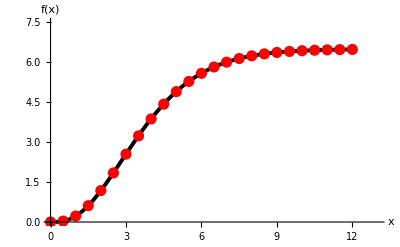

```mathematica
Max[Table[Abs[f[x]-f0[x]],{x,3,5,0.01}]]
F=Table[{x,f0[x]},{x,0,12,0.5}];
Show[Plot[f[x],{x,0,12}, PlotRange->{{0,13},{0,Pi^4/15+1}},PlotStyle->Directive[Black,Thickness[0.007]],AxesStyle->Directive[Black, 17,Arrowheads[.04]],
AxesLabel->{"x","f(x)"}], ListPlot[F, PlotStyle->Directive[Red, PointSize[0.02]]]]
```

```mathematica
T=27.282;
v1=10^17;
v0=0;
A*(f0[ (kHplank v1)/(kb T)]-f0[(kHplank v0)/(kb T)])T^4
kStefanBoltzmann/Pi T^4
```

General::munfl: Exp[-175745.] is too small to represent as a normalized machine number; precision may be lost.

10.0144

9.99923

```mathematica
R=0.3;
U[r_,kin_,kout_, Q_]:=Q Piecewise[{{1/2 NIntegrate[(1-Exp[-kin(2 √(R^2-r^2(1-μ^2)))])Exp[-kout(r μ-√(R^2-r^2(1-μ^2)))],{μ,√(1-(R/r)^2),1}],r≥R},{NIntegrate[1-Cosh[kin r μ]Exp[-kin √(R^2-r^2(1-μ^2))],{μ,0,1}],r<R}}]
X=Table[i,{i,0,1,0.01}];
{kC/(100*10^-7),kC/(800*10^-7), (kC/(100*10^-7)-kC/(800*10^-7))/20.}//N;
V=Table[v,{v,3.33*10^14,3.*10^15,(kC/(100*10^-7)-kC/(800*10^-7))/50.}];

Ie[T_,v1_,v0_]:=A*(f[ (kHplank v1)/(kb T)]-f[(kHplank v0)/(kb T)])T^4
absorp[d_,T_,v1_,v0_]:=d/(4 A*Pi*(f[ (kHplank v1)/(kb T)]-f[(kHplank v0)/(kb T)])T^4)
```

```mathematica
sol=Table[{V[[i]],U[R,absorp[10^-4,1000,V[[i+1]],V[[i]]],absorp[10^-100,1000,V[[i+1]],V[[i]]], Ie[1000,V[[i+1]],V[[i]]]]}, {i,1,Length[V]-1}];
```

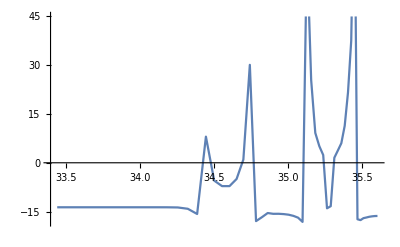

```mathematica
ListLinePlot[Log@sol]
```

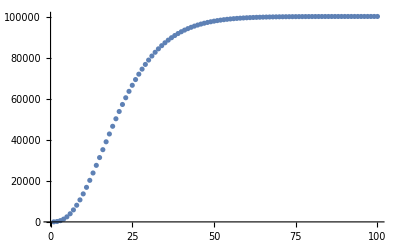

```mathematica
ListPlot[Table[Ie[273,x,0],{x,10^12,10^14,10^12}],PlotRange->All]
```

```mathematica
T=27.282;
v1=3*10^17;
v0=10^17;
Ie[T,v1,v0]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

-10.0144

```mathematica
q[x_]:=x^3+3 x^2+6x+7.28
IeLog[AA_,V0_,V1_]:= Log[A]-AA/2(V0+V1)+Log[Exp[AA/2(V1-V0)]q[V0]-Exp[-AA/2(V1-V0)]q[V1]]
```

```mathematica
IeLog[kHplank/(kb T),v0,v1]
```

General::munfl: Exp[-175745.] is too small to represent as a normalized machine number; precision may be lost.

-175640.

```mathematica
IeLog2[AA_,V0_,V1_]:= Log[A]-AA/2(V0+V1)+Log[Exp[AA/2(V1-V0)+Log[q[V0]]]-Exp[-AA/2(V1-V0)+Log[q[V1]]]]
IeLog2[kHplank/(kb T),v0,v1]
```

General::munfl: Exp[-175624.] is too small to represent as a normalized machine number; precision may be lost.

-175640.

```mathematica
IeLog3[AA_,V0_,V1_]:= Log[A]-AA/2(V0+V1)-AA/4(V1-V0)+Log[Exp[3/2 AA/2(V1-V0)+Log[q[V0]]]-Exp[-1/2 AA/2(V1-V0)+Log[q[V1]]]]
IeLog3[kHplank/(kb T),v0,v1]
```

General::munfl: Exp[-87751.7] is too small to represent as a normalized machine number; precision may be lost.

-175640.

```mathematica
3/2(kHplank/(kb T))/2(v1-v0)+Log[q[v0]]
```

263735.

```mathematica
q0[x_]:=x^3(1/3-x/8+x^2/62.4)
IeLog5[AA_,V0_,V1_]:= 
Piecewise[{{Log[A*(q0[AA*V1]-q0[AA*V0])],AA*V1≤2},{Piecewise[{{ Log[A]-AA/2(V0+V1)+Log[Exp[AA/2(V1-V0)]q[V0]-Exp[-AA/2(V1-V0)]q[V1]],AA/2(V1-V0)<700},{Log[A]-AA/2(V0+V1)+AA/2(V1-V0)+Log[q[V0]],AA/2(V1-V0)>=700}}],AA*V1>2}}]
```

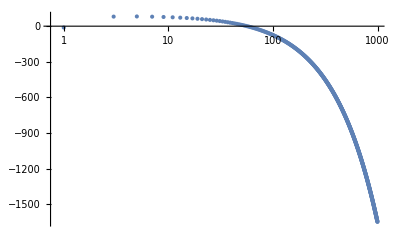

```mathematica
ListLogLinearPlot[Table[{x/10^14,Re@IeLog5[kHplank/(kb T*100),x-2*10^14,x]},{x,10^14,10^17,2*10^14}],PlotRange->All]
```

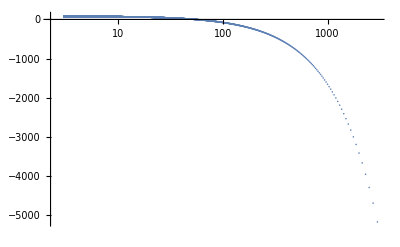

```mathematica
ListLogLinearPlot[Table[{(kC/λ)/10^14,IeLog5[kHplank/(kb T*100),kC/λ,kC/(λ-0.999*10^-7)]},{λ,1000*10^-7,0.1*10^-7,-0.1*10^-7}],PlotRange->All]
```

```mathematica
kStefanBoltzmann*T^4/Pi
Ie[T,10^14,0]
Exp[IeLog5[kHplank/(kb T),0,10^14]+4Log[T]]
```

9.99923

10.0144

11.2266

```mathematica
(*Ie[T_,v1_,v0_]:=A*(f[ (kHplank v1)/(kb T)]-f[(kHplank v0)/(kb T)])T^4*)
IeExp[AA_,V0_,V1_]:= A(Exp[-AA V0]q[V0]-Exp[-AA(V1)]q[V1])
IeExp[kHplank/(kb T),0,10^14]*T^4
Exp@IeLog5[kHplank/(kb T),0,10^20]*T^4
```

11.2266

11.2266

```mathematica
Table[x/10^14,{x,10^14,10^17,2*10^14}]//N ;
Table[λ,{λ,1000*10^-7,3*10^-7,-1*10^-7}]//N;
```

^2

```mathematica
Pi^4/15-q0[2]
```

5.31445

```mathematica
Pi^4/15-Exp[-2]*q[2]
```

1.17797

```mathematica
Log[5]//N
```

1.60944

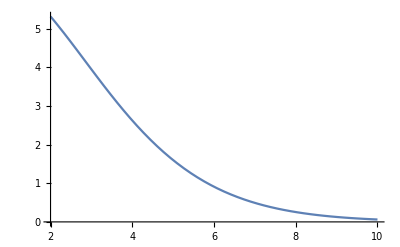

```mathematica
Plot[Exp[-x]*q[x],{x,2,10}]
```

```mathematica
(*
(*C++ расчёт*)
fplank=Import["/home/artem/projects/test/plank.txt","table"];
fplankL=Import["/home/artem/projects/test/plankL.txt","table"];
ListPlot[{fplank}]
ListPlot[Table[{fplank[[i,1]],(Exp@fplank[[i,2]])/(3 10^8)},{i,840,910}]]
Table[fplank[[i]],{i,950,Length@fplank}]
ListLogLogPlot[Table[{fplank[[i,1]],Exp@fplank[[i,2]]},{i,1,Length@fplank}]]*)
```

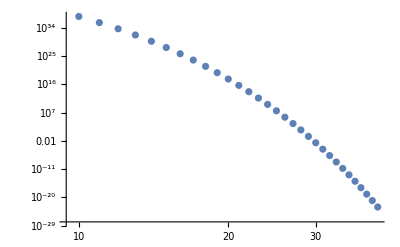

```mathematica
tem=10^4;
(*int[x,Inf]{sigmaT^4}*)
ListLogLogPlot[Table[{x/10^15,Exp[Re@IeLog5[kHplank/(kb tem),x,10^20]+4Log[tem]]},{x,10^16,4*10^16,10^15}],PlotRange->All]
```

```mathematica
(10^20-10^11)/1000//N
```

1.×10^17

-Graphics-

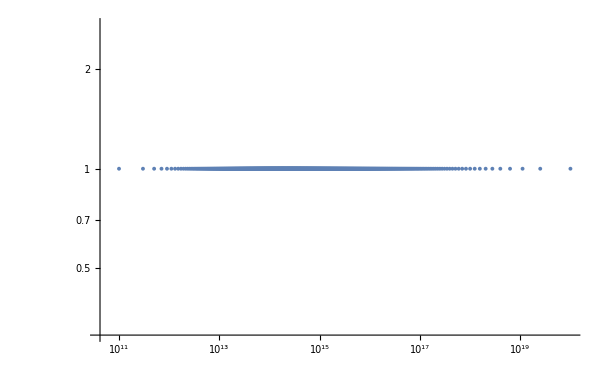

```mathematica
FF[x_]:=a 1/x^2+c
ans=NSolve[{FF[1]==10^20,FF[1000]==10^11},{a,c},Reals][[1]];
ListPlot[Table[{x,FF[x]/.ans},{x,1,1000}],PlotRange->All]
ListLogLogPlot[Table[{FF[x]/.ans,1},{x,1,1000}],PlotRange->All]
```

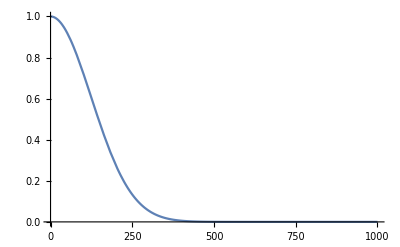

3.90469×10^-13

```mathematica
Plot[(a Exp[-x^2/b]+c)/.{a->1,b->31000,c->0},{x,0,1000},PlotRange->All]
(a Exp[-x^2/b]+c)/.{a->1,b->35000,c->0,x->1000}//N
```

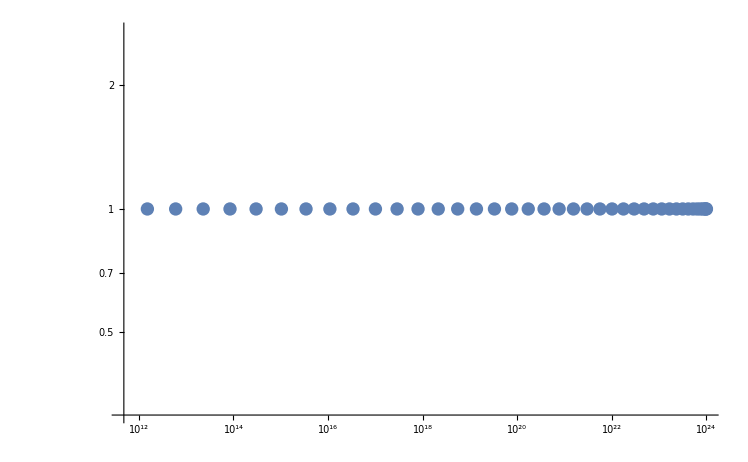

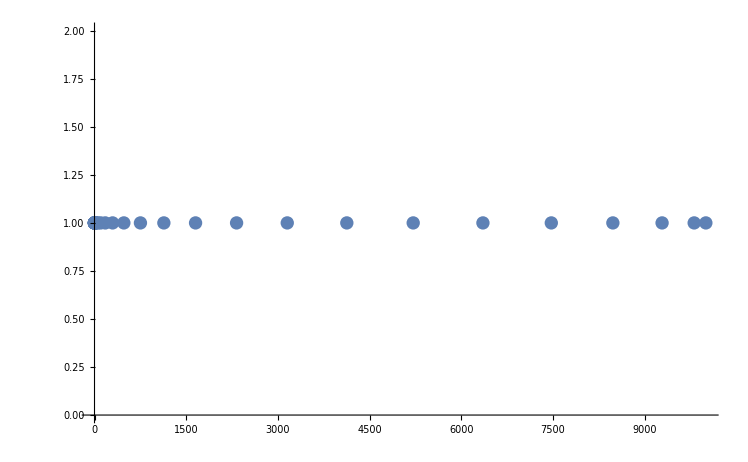

```mathematica
ListLogLogPlot[Table[{(a Exp[-x^2/b]+c)/.{a->10^24,b->35000,c->0},1},{x,1,1000,25}],PlotRange->All]
ListPlot[Table[{(a Exp[-x^2/b]+c)/10^20/.{a->10^24,b->35000,c->0},1},{x,1,1000,25}],PlotRange->All]
Spectr=Flatten@Table[{(a Exp[-x^2/b]+c)/.{a->10^24,b->35000,c->0}},{x,1,1000}]//N;
```

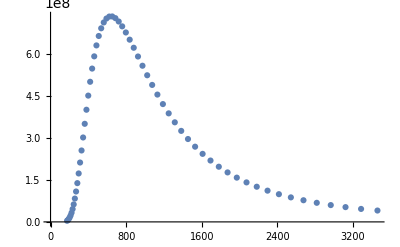

{{653.161,7.34763×10^8}}

```mathematica
(*Спектр Солнца*)
T=5780;
ListPlot[Table[{kC/10^-7/((Spectr[[x+1]]+Spectr[[x]])/2),Ie[T,Spectr[[x]],Spectr[[x+1]]]},{x,840,900}]]
MaximalBy[Table[{kC/10^-7/((Spectr[[x+1]]+Spectr[[x]])/2),Ie[T,Spectr[[x]],Spectr[[x+1]]]},{x,840,890}],Last]
```